# Finite Difference Methods

## Crank-Nicolson Scheme

Crank-Nicolson method for a potential step to the limiting current region for the reaction O + e ⇌ R.

Version 1.30
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[ListPlot3D,
AspectRatio-> 1,
AxesLabel->{
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["j",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["c  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Plain,FontWeight-> Bold]},
ImageSize->288,
ViewPoint->{2,-.5,1},
Mesh->False];
```

```mathematica
SetOptions[ListPlot,
Frame->True,
FrameStyle->AbsoluteThickness[1],
GridLines->None,
ImageSize->400,
PlotStyle->{Blue,AbsoluteThickness[1]},
Joined->True];
```

```mathematica
optionA={
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["z  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
None,
None},
FormatType-> TraditionalForm,
Frame-> False,
Joined-> False,
PlotRegion-> {{0,1},{0.1,0.9}},
PlotLabel-> None,
PlotStyle-> Thickness[0],
Prolog-> {Green,AbsolutePointSize[4.5]}
};
```

```mathematica
optionB={
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["z  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
None,
None},
FormatType-> TraditionalForm,
Frame-> False,
Joined-> True,
PlotRegion-> {{0,1},{0.1,0.9}},
PlotLabel-> None,
PlotStyle-> {Red,Thickness[0.002]}};
```

```mathematica
$Line=0;
```

## Make Diagonals and Matrix

```mathematica
Clear[makeCrankDiagonals];

makeCrankDiagonals[m_Integer,d_]:=
	Module[{x,y,z},
		x=Table[-1,{m-3}];
		z=Table[-1,{m-3}];
		y=Table[2.+2./d,{m-2}];
{x,y,z}]
```

```mathematica
{x,y,z}=makeCrankDiagonals[7,𝔻]
```

{{-1,-1,-1,-1},{2.+2./𝔻,2.+2./𝔻,2.+2./𝔻,2.+2./𝔻,2.+2./𝔻},{-1,-1,-1,-1}}

```mathematica
SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},5]
```

SparseArray[…]

```mathematica
Clear[makeMatrix];
makeMatrix[x_,y_,z_]:=Module[{n=Length[y]},
SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},n]
]
```

```mathematica
MatrixForm[makeMatrix[x,y,z]]
```

(2.+2./𝔻 | -1 | 0 | 0 | 0
-1 | 2.+2./𝔻 | -1 | 0 | 0
0 | -1 | 2.+2./𝔻 | -1 | 0
0 | 0 | -1 | 2.+2./𝔻 | -1
0 | 0 | 0 | -1 | 2.+2./𝔻)

## Set Up Solution

#### LinearSolve Solution

```mathematica
Clear[crankSolve];

crankSolve[m_Integer,n_Integer,d_]:=Module[{x,y,z,len,mat,initial,solveNext},
{x,y,z}=makeCrankDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
initial=ConstantArray[1.,{m}];
solveNext:=Module[{b},
b=ListCorrelate[{1.,-2.+2./d,1.},#];
b[[-1]]=b[[-1]]+1.;
Flatten[{0.,LinearSolve[mat,b],1.}]]&;

NestList[solveNext,initial,n-1]]
```

## Set Parameter Values

```mathematica
Clear[𝒟,time,n,m,Δt,Δx,𝔻,c];

𝒟=10^-5;(*diffusion coefficient*)
time=0.1;
n=400;
𝔻=2.;(*model diffusion coefficient*)
m=Ceiling[6*√(𝔻*(n-1))];
Δt=time/n//N;
Δx=√((𝒟*Δt)/𝔻);
```

## Solve

```mathematica
Clear[c];

Timing[
c=crankSolve[m,n,𝔻];
c=Rest[c];]
```

{0.085419,Null}

Comparison with analytical result:

```mathematica
With[{p=40(*enter a time increment*),Δx=√((𝒟*Δt)/𝔻)},
Table[Erf[(j*Δx)/(2*Sqrt[𝒟*Δt*p])]/c⟦p,j+1⟧,{j,2,m-1}]
]
```

{0.993567,0.993641,0.993743,0.993873,0.994028,0.994207,0.994408,0.994629,0.994868,0.995121,0.995387,0.995661,0.995942,0.996226,0.996511,0.996793,0.997071,0.997341,0.997602,0.997851,0.998088,0.99831,0.998517,0.998708,0.998883,0.999041,0.999183,0.99931,0.999421,0.999519,0.999603,0.999675,0.999737,0.999789,0.999832,0.999867,0.999896,0.99992,0.999939,0.999953,0.999965,0.999974,0.999981,0.999986,0.99999,0.999993,0.999995,0.999997,0.999998,0.999999,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

## Plot current v. time

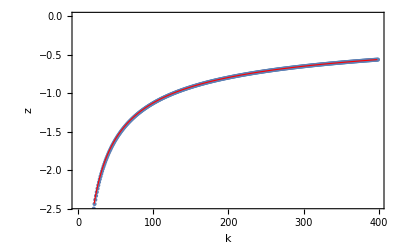

```mathematica
Clear[i,z];
i=Map[((-4*#⟦2⟧+#⟦3⟧)*0.5*√(𝔻*(n-1)))&,c];

z=Table[-1/Sqrt[Pi*(k-1)/(n-1)],{k,2,n-1}];

Show[ListPlot[i,optionA],ListPlot[z,optionB]]
```

## Plot concentration profiles

```mathematica
ListPlot3D[Transpose@c,PlotRange->All]
```

-Graphics3D-